## 第一小题

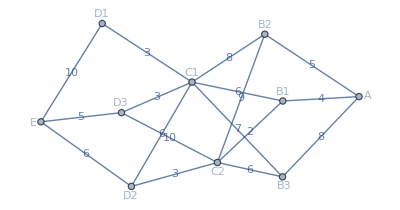

```mathematica
(*定义顶点*)vertices={"A","B1","B2","B3","C1","C2","D1","D2","D3","E"};

(*定义边及其权重*)
edges={"A"<->"B2","A"<->"B1","A"<->"B3","B1"<->"C1","B1"<->"C2","B2"<->"C1","B2"<->"C2","B3"<->"C2","B3"<->"C1","C1"<->"D1","C1"<->"D2","C1"<->"D3","C2"<->"D2","C2"<->"D3","D1"<->"E","D2"<->"E","D3"<->"E"};

(*定义边的权重*)
weights={5,4,8,6,2,8,9,6,7,3,6,3,3,10,10,6,5};

(*创建加权图*)
g=Graph[vertices,UndirectedEdge@@@edges,EdgeWeight->weights,VertexLabels->"Name",EdgeLabels->Placed["EdgeWeight",Center],GraphLayout->"SpringEmbedding"];

(*显示图*)
g
```

## 第二小题

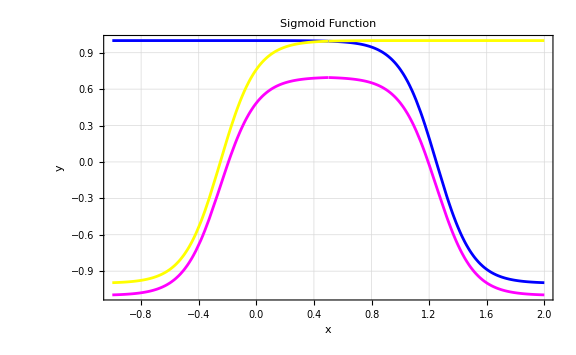

```mathematica
(*定义 x 的范围*)x=Range[-1,2,0.01];

(*定义 Sigmoid 函数*)
sigmoid1[x_]:=2/(1+Exp[8(x-1.25)])-1;
sigmoid2[x_]:=2/(1+Exp[8((1-x)-1.25)])-1;
y2[x_]:=Which[x>0.5,0.9*sigmoid1[x]-0.2,x<=0.5,0.9*sigmoid2[x]-0.2];
(*绘图*)
Plot[{sigmoid1[x],sigmoid2[x],y2[x]},{x,-1,2},PlotStyle->{Blue,Yellow,Magenta},AxesOrigin->{0,0},GridLines->Automatic,Frame->True,FrameLabel->{"x","y"},PlotLabel->"Sigmoid Function",ImageSize->Large]
```